```mathematica
r1=10;
r2=10;
a1=Pi/4;
a2=Pi/3;
m1=4;
m2=3;
g=28.8;
timestep=0.1;
{x1,y1}={r1*Sin[a1],-r1*Cos[a1]};
{x2,y2}={x1+r2*Sin[a2],y1-r2*Cos[a2]};
w1=0.3;
w2=2.3;
lp={{0,0},{x1,y1},{x2,y2}};
englist={};
Do[
{
Subscript[p, t]=Show[ListPlot[lp,PlotStyle->PointSize[0.03],PlotRange->{{-1.5(r1+r2),1.5(r1+r2)},{-1.5(r1+r2),1.5(r1+r2)}},PlotRange->{{-20,20},{-20,20}},AspectRatio->1],ListLinePlot[lp,PlotRange->{{-20,20},{-20,20}}]],
al1= (−g (2*m1+m2) *Sin [a1]−m2* g *Sin[a1−2 *a2]−2 *Sin[a1−a2]* m2 *(w2^2 *r2+w1^2* r1 *Cos[a1−a2]))/(r1 *(2* m1+m2−m2 *Cos[2 *a1−2 a2])),
al2=(2 *Sin[a1−a2] *(w1^2 *r1 *(m1+m2)+g*(m1+m2)* Cos [a1]+w2^2* r2* m2* Cos[a1−a2]))/(r2 *(2 m1+m2−m2 *Cos[2 a1−2 a2])), 
w1=w1+timestep*al1,
w2=w2+timestep*al2,
a1=a1+timestep*w1,
a2=a2+timestep*w2,
{x10,y10}={x1,y1},
{x20,y20}={x2,y2},
{x1,y1}={r1*Sin[a1],-r1*Cos[a1]},
{x2,y2}={x1+r2*Sin[a2],y1-r2*Cos[a2]},
lp=Drop[lp,{-2,-1}],
AppendTo[lp,{x1,y1}],
AppendTo[lp,{x2,y2}],
KE1=1/2*m1*(((x1-x10)/timestep)^2+((y1-y10)/timestep)^2),
PE1=-m1*28.8*(-20-y1),
KE2=1/2*m2*(((x2-x20)/timestep)^2+((y2-y20)/timestep)^2),
PE2=-m2*28.8*(-20-y2),
AppendTo[englist,PE1],
Subscript[p2, t]=ListPlot[englist,Joined->True]
}
,{t,1,30,timestep}]
gif1=Table[Subscript[p, t],{t,1,30,timestep}];
gif2=Table[Subscript[p2, t],{t,1,30,timestep}];
Export["E:\\test_gif(1).gif",gif1];
Export["E:\\test_gif(2).gif",gif2];
SystemOpen["E:\\test_gif(1).gif"];
SystemOpen["E:\\test_gif(2).gif"];
```

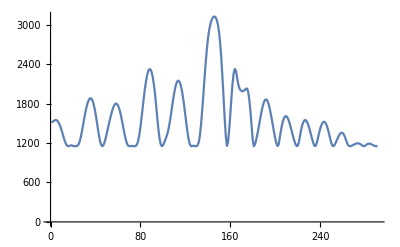

```mathematica
ListLinePlot[englist]
```

```mathematica
NDSol
```